```mathematica
Clear["Global`*"]
```

```mathematica
L=100;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

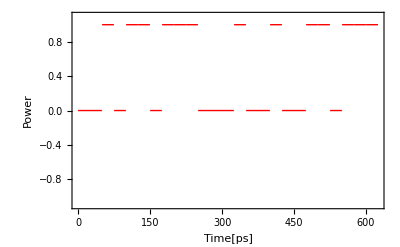

-1/(2 f π)ⅈ ⅇ^(-1250 ⅈ f π) (-1+ⅇ^(150 ⅈ f π)-ⅇ^(200 ⅈ f π)+ⅇ^(300 ⅈ f π)-ⅇ^(400 ⅈ f π)+ⅇ^(450 ⅈ f π)-ⅇ^(550 ⅈ f π)+ⅇ^(600 ⅈ f π)-ⅇ^(750 ⅈ f π)+ⅇ^(900 ⅈ f π)-ⅇ^(950 ⅈ f π)+ⅇ^(1050 ⅈ f π)-ⅇ^(1100 ⅈ f π)+ⅇ^(1150 ⅈ f π))

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
bit=25;
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25<t<(i+1)*25,1,0],If[i*25<t<(i+1)*25,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
∫_0^(bit*25) signal[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

Cos[400 π t]

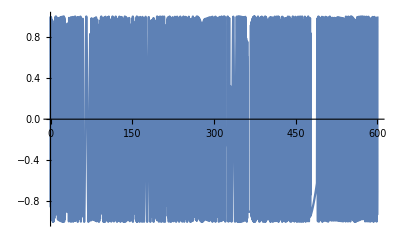

Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0])

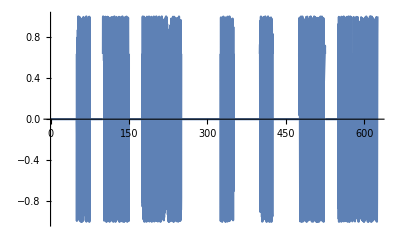

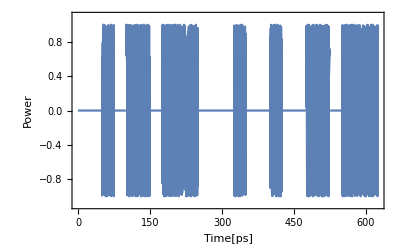

ⅈ Im[∫_0^625 ⅇ^(-2 ⅈ f π t1) cs[t1]ⅆt1]+Re[∫_0^625 ⅇ^(-2 ⅈ f π t1) cs[t1]ⅆt1]

```mathematica
Fc= 200 ;(*搬送波の周波数[THz]*)
carrier[t]= Cos[2*Pi*Fc*t]
Plot[carrier[t], {t,0,600}]
cs[t_]=signal[t]*carrier[t]
Plot[Evaluate[cs[t]],{t,0,bit*25}]
Plot[Evaluate[cs[t]],{t,0,bit*25},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
ComplexExpand[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
```

```mathematica
Evaluate[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
ComplexExpand[Integratepaclet:ref/Integrate[cs[t]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,625}]]
Nintegrate[cs[t]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,625}]
```

∫_0^625 ⅇ^(-2 ⅈ f π t1) cs[t1]ⅆt1

Rule::rhs: パターンpaclet:ref/Integrateは規則System`ComplexExpandDump`reimexpr[RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) «1» (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+«5»+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),«1»]]«1»«1»の右辺にあります．

RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),{t,0,625}]

Nintegrate[ⅇ^(-2 ⅈ f π t1) Cos[400 π t] (If[25<t<50,0,0]+If[50<t<75,1,0]+If[75<t<100,0,0]+If[100<t<125,1,0]+If[125<t<150,1,0]+If[150<t<175,0,0]+If[175<t<200,1,0]+If[200<t<225,1,0]+If[225<t<250,1,0]+If[250<t<275,0,0]+If[275<t<300,0,0]+If[300<t<325,0,0]+If[325<t<350,1,0]+If[350<t<375,0,0]+If[375<t<400,0,0]+If[400<t<425,1,0]+If[425<t<450,0,0]+If[450<t<475,0,0]+If[475<t<500,1,0]+If[500<t<525,1,0]+If[525<t<550,0,0]+If[550<t<575,1,0]+If[575<t<600,1,0]+If[600<t<625,1,0]+If[625<t<650,1,0]),{t,0,625}]

```mathematica
Cs[f]=ComplexExpand[FourierTransform[cs[t],t,2*Pi*f]]
(*Cs[ω]:=1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω])*)
(*Plot[Re[FourierTransform[cs[t],t,ω]],{ω,-100,100}]*)
(*Plot[Evaluate[[Re[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]]],{f,-100,100}]*)
```

ⅈ ((f Cos[100 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[150 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[200 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[300 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[350 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[500 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[650 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[700 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[800 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[850 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[950 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[1050 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[1100 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[1300 f π])/(2 √2 (-40000+f^2) π^(3/2)))-(f Sin[100 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[150 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[200 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[300 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[350 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[500 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[650 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[700 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[800 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[850 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[950 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[1050 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[1100 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[1300 f π])/(2 √2 (-40000+f^2) π^(3/2))

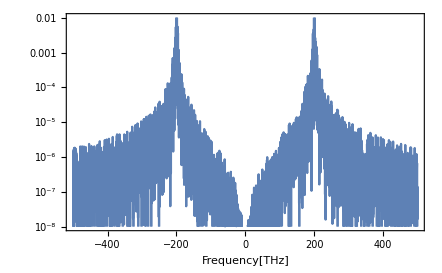

```mathematica
LogPlot[(Re[Cs[f]]^2+Im[Cs[f]]^2),{f,-0.5*10^3,0.5*10^3},Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{10^-8,10^-2}]
```

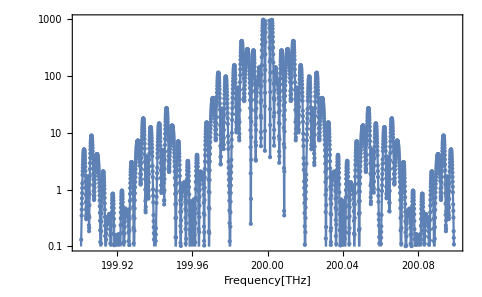

```mathematica
LogPlot[(Re[Cs[f]]^2+Im[Cs[f ]]^2),{f,1.999*10^2,2.001*10^2},Mesh->All,Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{10^-1,10^3}]
```

```mathematica
H_dis[f]:=Exp[-1/2*I(f-Fc)^2*(2*pi)^2*β2*L]
(*FourierTransform[Exp[-1/2*I(ω-2*Pi*Fc)^2*β2*L]*1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω]),ω,t,FourierParameters->{1,-1}]*)
(*Cs_dis[t]=ComplexExpand[FourierTransform[H_dis[f]*Cs[f],f,t,FourierParameters->{1,-1}]]*)
```

```mathematica
(*FourierTransform[ⅇ^((0.-1.0196526687420762*^-21 ⅈ) (-400 π+ω)^2)*1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω]),ω,t,FourierParameters->{1,-1}]*)
```

```mathematica
(*Plot[FourierTransform[ⅇ^((0.-1.0196526687420762*^-21 ⅈ) (-400 π+ω)^2)*1/(√(2 π) (-160000 π^2+ω^2))ω (ⅈ Cos[50 ω]-ⅈ Cos[75 ω]+ⅈ Cos[100 ω]-ⅈ Cos[150 ω]+ⅈ Cos[175 ω]-ⅈ Cos[250 ω]+ⅈ Cos[325 ω]-ⅈ Cos[350 ω]+ⅈ Cos[400 ω]-ⅈ Cos[425 ω]+ⅈ Cos[475 ω]-ⅈ Cos[525 ω]+ⅈ Cos[550 ω]-ⅈ Cos[650 ω]-Sin[50 ω]+Sin[75 ω]-Sin[100 ω]+Sin[150 ω]-Sin[175 ω]+Sin[250 ω]-Sin[325 ω]+Sin[350 ω]-Sin[400 ω]+Sin[425 ω]-Sin[475 ω]+Sin[525 ω]-Sin[550 ω]+Sin[650 ω]),ω,t,FourierParameters->{1,-1}],{t,-100,100}]*)
```